# Dynamics of a system of trapped Ions inside two fiber-coupled optical cavities in a one excitation Hilbert space

## 1. Liouvillian Matrix

The Liouvillian matrix obtained is the following

```mathematica
Clear[L0,γ,α,χ,κ,gef]
L0=({{-γ-χ, -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, χ, γ, 0, 0, 0}, {-α, 1/2 (-γ-κ-χ), 0, α, 0, 0, 0, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {α, 0, 1/2 (-γ-κ-χ), -α, 0, 0, 0, 0, -α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, α, -α, -κ, -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, κ}, {0, 0, 0, -α, 1/2 (-γ-κ-χ), 0, α, 0, -α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, α, 0, 1/2 (-γ-κ-χ), -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, α, -α, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, χ, γ, 0}, {0, α, 0, 0, 0, α, 0, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -α, 0, -α, 0, 0, 0, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, 0, 0, α, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, 0, 0, -α, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, -α, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, α, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, α, 0, -α, 0, -κ/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -α, 0, α, 0, -κ/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0, 0, 0, γ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ, 0, 0, χ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0, γ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ, χ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

For the vector basis of elements of the density operator

```mathematica
v0 = {M[1,1,0,0,0,1,1,0,0,0],M[1,1,0,0,0,0,0,0,0,1],M[0,0,0,0,1,1,1,0,0,0],M[0,0,0,0,1,0,0,0,0,1],M[0,0,1,1,0,0,0,0,0,1],M[0,0,0,0,1,0,0,1,1,0],M[0,0,1,1,0,0,0,1,1,0],M[1,1,0,0,0,0,0,1,1,0],M[0,0,1,1,0,1,1,0,0,0],M[1,1,0,0,0,0,0,0,0,0],M[0,0,0,0,0,1,1,0,0,0],M[0,0,1,1,0,0,0,0,0,0],M[0,0,0,0,0,0,0,1,1,0],M[0,0,0,0,1,0,0,0,0,0],M[0,0,0,0,0,0,0,0,0,1],M[1,0,0,0,0,1,0,0,0,0],M[0,1,0,0,0,0,1,0,0,0],M[0,0,1,0,0,0,0,1,0,0],M[0,0,0,1,0,0,0,0,1,0],M[0,0,0,0,0,0,0,0,0,0]};
```

But the matrix L0 is singular and consequently not invertible. We can’t determine MatrixExp[L0 t] to obtain the solution for the dynamics of our system. To contour this, we can remove the last row (full of zeros) and column of the matrix L0 and obtain the new non-singular matrix L. Notice that if γ = χ = 0, the matrix is singular and we need to remove the last 4 rows and columns.

```mathematica
Clear[L,γ,α,χ,κ,gef];α = -I gef;
L=({{-γ-χ, -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, χ, γ, 0, 0}, {-α, 1/2 (-γ-κ-χ), 0, α, 0, 0, 0, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {α, 0, 1/2 (-γ-κ-χ), -α, 0, 0, 0, 0, -α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, α, -α, -κ, -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -α, 1/2 (-γ-κ-χ), 0, α, 0, -α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, α, 0, 1/2 (-γ-κ-χ), -α, α, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, α, -α, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, χ, γ}, {0, α, 0, 0, 0, α, 0, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -α, 0, -α, 0, 0, 0, -γ-χ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, 0, 0, α, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, 0, 0, -α, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, -α, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 (-γ-χ), 0, α, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, α, 0, -α, 0, -κ/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -α, 0, α, 0, -κ/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ}});
L//MatrixForm
```

(-γ-χ | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | χ | γ | 0 | 0
ⅈ gef | 1/2 (-γ-κ-χ) | 0 | -ⅈ gef | 0 | 0 | 0 | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ gef | 0 | 1/2 (-γ-κ-χ) | ⅈ gef | 0 | 0 | 0 | 0 | ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ gef | ⅈ gef | -κ | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ gef | 1/2 (-γ-κ-χ) | 0 | -ⅈ gef | 0 | ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ gef | 0 | 1/2 (-γ-κ-χ) | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ gef | ⅈ gef | -γ-χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | χ | γ
0 | -ⅈ gef | 0 | 0 | 0 | -ⅈ gef | 0 | -γ-χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ gef | 0 | ⅈ gef | 0 | 0 | 0 | -γ-χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-γ-χ) | 0 | 0 | 0 | -ⅈ gef | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-γ-χ) | 0 | 0 | 0 | ⅈ gef | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-γ-χ) | 0 | ⅈ gef | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-γ-χ) | 0 | -ⅈ gef | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ gef | 0 | ⅈ gef | 0 | -κ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ gef | 0 | -ⅈ gef | 0 | -κ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -χ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -χ)

With new vector basis

```mathematica
v = {M1100011000[t],M1100000001[t],M0000111000[t],M0000100001[t],M0011000001[t],M0000100110[t],M0011000110[t],M1100000110[t],M0011011000[t],M1100000000[t],M0000011000[t],M0011000000[t],M0000000110[t],M0000100000[t],M0000000001[t],M1000010000[t],M0100001000[t],M0010000100[t],M0001000010[t]};
```

## 2. Initial state

The initial state in this basis will be

```mathematica
v = {M1100011000[t],M1100000001[t],M0000111000[t],M0000100001[t],M0011000001[t],M0000100110[t],M0011000110[t],M1100000110[t],M0011011000[t],M1100000000[t],M0000011000[t],M0011000000[t],M0000000110[t],M0000100000[t],M0000000001[t],M1000010000[t],M0100001000[t],M0010000100[t],M0001000010[t]};
vi[θ_,ϕ_] = {Cos[θ]^2,0,0,0,0,0,0,0,0,Exp[-I ϕ] Cos[θ]Sin[θ],Exp[I ϕ] Cos[θ]Sin[θ],0,0,0,0,0,0,0,0};
initial=vi[π/4,0]
```

{1/2,0,0,0,0,0,0,0,0,1/2,1/2,0,0,0,0,0,0,0,0}

## 3. Splitting the Liouvillian Matrices

```mathematica
M1 =({{-γ-χ, ⅈ gef, -ⅈ gef, 0, 0, 0, 0, 0, 0, χ, γ, 0, 0}, {ⅈ gef, 1/2 (-γ-κ-χ), 0, -ⅈ gef, 0, 0, 0, -ⅈ gef, 0, 0, 0, 0, 0}, {-ⅈ gef, 0, 1/2 (-γ-κ-χ), ⅈ gef, 0, 0, 0, 0, ⅈ gef, 0, 0, 0, 0}, {0, -ⅈ gef, ⅈ gef, -κ, ⅈ gef, -ⅈ gef, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅈ gef, 1/2 (-γ-κ-χ), 0, -ⅈ gef, 0, ⅈ gef, 0, 0, 0, 0}, {0, 0, 0, -ⅈ gef, 0, 1/2 (-γ-κ-χ), ⅈ gef, -ⅈ gef, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -ⅈ gef, ⅈ gef, -γ-χ, 0, 0, 0, 0, χ, γ}, {0, -ⅈ gef, 0, 0, 0, -ⅈ gef, 0, -γ-χ, 0, 0, 0, 0, 0}, {0, 0, ⅈ gef, 0, ⅈ gef, 0, 0, 0, -γ-χ, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -γ, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -χ}}); M1 //MatrixForm
(* Basis vector *)
B1 = {v[[1]],v[[2]],v[[3]],v[[4]],v[[5]],v[[6]],v[[7]],v[[8]],v[[9]],v[[16]],v[[17]],v[[18]],v[[19]]} 
(* Initial state in this basis *)
B10 = {initial[[1]],initial[[2]],initial[[3]],initial[[4]],initial[[5]],initial[[6]],initial[[7]],initial[[8]],initial[[9]],initial[[16]],initial[[17]],initial[[18]],initial[[19]]} 

M2=({{1/2 (-γ-χ), 0, 0, 0, -ⅈ gef, 0}, {0, 1/2 (-γ-χ), 0, 0, 0, ⅈ gef}, {0, 0, 1/2 (-γ-χ), 0, ⅈ gef, 0}, {0, 0, 0, 1/2 (-γ-χ), 0, -ⅈ gef}, {-ⅈ gef, 0, ⅈ gef, 0, -κ/2, 0}, {0, ⅈ gef, 0, -ⅈ gef, 0, -κ/2}}); M2 //MatrixForm
(* Basis vector *)
B2 = {v[[10]],v[[11]],v[[12]],v[[13]],v[[14]],v[[15]]}
(* Initial state in this basis *)
B20 = {initial[[10]],initial[[11]],initial[[12]],initial[[13]],initial[[14]],initial[[15]]}
```

(-γ-χ | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | χ | γ | 0 | 0
ⅈ gef | 1/2 (-γ-κ-χ) | 0 | -ⅈ gef | 0 | 0 | 0 | -ⅈ gef | 0 | 0 | 0 | 0 | 0
-ⅈ gef | 0 | 1/2 (-γ-κ-χ) | ⅈ gef | 0 | 0 | 0 | 0 | ⅈ gef | 0 | 0 | 0 | 0
0 | -ⅈ gef | ⅈ gef | -κ | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ gef | 1/2 (-γ-κ-χ) | 0 | -ⅈ gef | 0 | ⅈ gef | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ gef | 0 | 1/2 (-γ-κ-χ) | ⅈ gef | -ⅈ gef | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ gef | ⅈ gef | -γ-χ | 0 | 0 | 0 | 0 | χ | γ
0 | -ⅈ gef | 0 | 0 | 0 | -ⅈ gef | 0 | -γ-χ | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ gef | 0 | ⅈ gef | 0 | 0 | 0 | -γ-χ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -χ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -χ)

{M1100011000[t],M1100000001[t],M0000111000[t],M0000100001[t],M0011000001[t],M0000100110[t],M0011000110[t],M1100000110[t],M0011011000[t],M1000010000[t],M0100001000[t],M0010000100[t],M0001000010[t]}

{1/2,0,0,0,0,0,0,0,0,0,0,0,0}

(1/2 (-γ-χ) | 0 | 0 | 0 | -ⅈ gef | 0
0 | 1/2 (-γ-χ) | 0 | 0 | 0 | ⅈ gef
0 | 0 | 1/2 (-γ-χ) | 0 | ⅈ gef | 0
0 | 0 | 0 | 1/2 (-γ-χ) | 0 | -ⅈ gef
-ⅈ gef | 0 | ⅈ gef | 0 | -κ/2 | 0
0 | ⅈ gef | 0 | -ⅈ gef | 0 | -κ/2)

{M1100000000[t],M0000011000[t],M0011000000[t],M0000000110[t],M0000100000[t],M0000000001[t]}

{1/2,1/2,0,0,0,0}

## 4. Solving the dynamics

```mathematica
Clear[sol1,sol2]
sol1 = MatrixExp[M1 t].B10
sol2 = MatrixExp[M2 t].B20
```

{1/2 (-1/1 ⅇ^(1/2 t (-γ-κ-χ+√(-32 gef^2+(γ-κ+χ)^2))) (((-(16 ⅈ gef)/(-γ+κ-χ+√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))-(16 ⅈ gef)/(γ-κ+χ+√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-1-1) (-4 (-(ⅈ (1) (2+1))/gef+4 (1-1))-1/1)+1) 1-1)+6+ⅇ^(-t (γ+χ)) (1/2-(((-32 gef^2+11+χ √1)/(16 gef^2)+1/1+(2 √1 (1))/((1) 1)) 1)/(((-(16 ⅈ gef)/(-γ+κ-χ+√1)-(16 ⅈ gef)/1) (1) (-4 (1)-1)+1) 1-1))),1/2 (1),1/2 1,7,0,0,0}
 |  |  |  |

{1/2 ((ⅇ^(1/2 t (-γ-χ)) (-4 gef^2+1/4 (-γ+κ-χ-√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)) (-γ+κ-χ+√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))))/(8 gef^2)-(4 ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)-(4 ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)),1/2 ((ⅇ^(1/2 t (-γ-χ)) (-4 gef^2+1/4 (-γ+κ-χ-√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)) (-γ+κ-χ+√(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))))/(8 gef^2)-(4 ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)-(4 ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)),1/2 (1/2 ⅇ^(1/2 t (-γ-χ))+(4 ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)+(4 ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)),1/2 (1/2 ⅇ^(1/2 t (-γ-χ))+(4 ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)+(4 ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) gef^2)/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)),1/2 ((ⅈ ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) (-gef γ+gef κ-gef χ+gef √(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)+(ⅈ ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) (-gef γ+gef κ-gef χ-gef √(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)),1/2 ((ⅈ ⅇ^(1/4 t (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) (gef γ-gef κ+gef χ-gef √(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ-√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2)+(ⅈ ⅇ^(1/4 t (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))) (gef γ-gef κ+gef χ+gef √(-32 gef^2+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))/(8 gef^2+γ^2+2 γ κ+2 γ χ+2 κ χ+χ^2+1/2 (4 γ+2 κ+4 χ) (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))+3/4 (-γ-κ-χ+√((γ+κ+χ)^2-4 (8 gef^2+γ κ+κ χ)))^2))}

```mathematica
gef=1;
M1100011000[t_,γ_,χ_,κ_]=sol1[[1]];(* Diagonal, Real *)
M1100000001[t_,γ_,χ_,κ_]=sol1[[2]];
M0000111000[t_,γ_,χ_,κ_]=sol1[[3]]; (* Conjugate of expression above *)
M0000100001[t_,γ_,χ_,κ_]=sol1[[4]];(* Diagonal, Real *)
M0011000001[t_,γ_,χ_,κ_]=sol1[[5]];
M0000100110[t_,γ_,χ_,κ_]=sol1[[6]]; (* Conjugate of expression above *)
M0011000110[t_,γ_,χ_,κ_]=sol1[[7]];(* Diagonal, Real *)
M1100000110[t_,γ_,χ_,κ_]=sol1[[8]];
M0011011000[t_,γ_,χ_,κ_]=sol1[[9]]; (* Conjugate of expression above *)
M1100000000[t_,γ_,χ_,κ_]=Exp[I ω t]sol2[[1]];
M0000011000[t_,γ_,χ_,κ_]=Exp[-I ω t]sol2[[2]]; (* Conjugate of expression above *)
M0011000000[t_,γ_,χ_,κ_]=Exp[I ω t]sol2[[3]];
M0000000110[t_,γ_,χ_,κ_]=Exp[-I ω t]sol2[[4]]; (* Conjugate of expression above *)
M0000100000[t_,γ_,χ_,κ_]=Exp[I ω t]sol2[[5]];
M0000000001[t_,γ_,χ_,κ_]=Exp[-I ω t]sol2[[6]]; (* Conjugate of expression above *)
M1000010000[t_,γ_,χ_,κ_]=sol1[[10]]; (* Diagonal, Real *)
M0100001000[t_,γ_,χ_,κ_]=sol1[[11]];(* Diagonal, Real *)
M0010000100[t_,γ_,χ_,κ_]=sol1[[12]];(* Diagonal, Real *)
M0001000010[t_,γ_,χ_,κ_]=sol1[[13]]; (* Diagonal, Real *)
M0000000000[t_,γ_,χ_,κ_]=1-sol1[[1]]-sol1[[4]]-sol1[[7]]-sol1[[10]]-sol1[[11]]-sol1[[12]]-sol1[[13]]; (* Diagonal, Real *)
```

```mathematica
(* Reduced Density matrix of ion 1 *)
ρ1=Table[0,{i,4},{j,4}];
ρ1[[1,1]] = Simplify[M0000000000[t,γ,χ,κ]+M0011000110[t,γ,χ,κ]+M0000100001[t,γ,χ,κ]+M0010000100[t,γ,χ,κ]+M0001000010[t,γ,χ,κ]];
ρ1[[2,2]] = Simplify[M0100001000[t,γ,χ,κ]];
ρ1[[3,3]] = Simplify[M1000010000[t,γ,χ,κ]];
ρ1[[4,4]] = Simplify[M1100011000[t,γ,χ,κ]];
ρ1[[1,4]] = Simplify[M0000011000[t,γ,χ,κ]];
ρ1[[4,1]] =Conjugate[ρ1[[1,4]]];
```

```mathematica
(* Partial Transpose of ρ1 *)
ρ1T2=Table[0,{i,4},{j,4}];
ρ1T2[[1,1]] = ρ1[[1,1]];
ρ1T2[[2,2]] = ρ1[[2,2]];
ρ1T2[[3,3]] = ρ1[[3,3]];
ρ1T2[[4,4]] = ρ1[[4,4]];
ρ1T2[[1,4]] = ρ1[[2,3]];
ρ1T2[[2,3]] =ρ1[[1,4]];
ρ1T2[[4,1]] = Conjugate[ρ1T2[[1,4]]];
ρ1T2[[3,2]] =Conjugate[ρ1T2[[2,3]]];
(* Eigenvalues of ρ1T2 *)
eigenT1=Eigenvalues[ρ1T2]
```

{(4 ⅇ^1 1 (32768 ⅇ^(t (γ+χ)+1/2 t (γ+κ+χ)+1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2)))+8192 ⅇ^(t (γ+χ)+1+1/4 t (1))+16384 ⅇ^1+507+1+2 ⅇ^1 χ^5 √(-32+(γ-κ+χ)^2)+ⅇ^(t (γ+χ)+1/2 t (γ+κ+χ)+1/2 t (1)+1/2 t (γ+κ+χ+√(-32+1))+1/4 t (3 γ+κ+3 χ+√(-32+(γ-κ+χ)^2))) χ^5 √(-32+(γ-κ+χ)^2)))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)^(3/2) (γ-κ+χ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)) (32-γ^2+11+χ √1)^2 (-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2+γ √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)-κ √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)+χ √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))),-1/1,1,(ⅈ 2 √Conjugate[1])/(√1 √1)}
 |  |  |  |

```mathematica
(* Reduced Density matrix of ion 2 *)
ρ2=Table[0,{i,4},{j,4}];
ρ2 [[1,1]] = Simplify[M0000000000[t,γ,χ,κ]+M1100011000[t,γ,χ,κ]+M0000100001[t,γ,χ,κ]+M1000010000[t,γ,χ,κ]+M0100001000[t,γ,χ,κ]];
ρ2[[2,2]] = Simplify[M0001000010[t,γ,χ,κ]];
ρ2[[3,3]] = Simplify[M0010000100[t,γ,χ,κ]];
ρ2[[4,4]] = Simplify[M0011000110[t,γ,χ,κ]];
ρ2[[1,4]] = Simplify[M0000000110[t,γ,χ,κ]];
ρ2[[4,1]] =Conjugate[ρ2[[1,4]]];
```

```mathematica
(* Partial Transpose of ρ2 *)
ρ2T2=Table[0,{i,4},{j,4}];
ρ2T2[[1,1]] = ρ2[[1,1]];
ρ2T2[[2,2]] = ρ2[[2,2]];
ρ2T2[[3,3]] = ρ2[[3,3]];
ρ2T2[[4,4]] = ρ2[[4,4]];
ρ2T2[[1,4]] = ρ2[[2,3]];
ρ2T2[[2,3]] =ρ2[[1,4]];
ρ2T2[[4,1]] = Conjugate[ρ2T2[[1,4]]];
ρ2T2[[3,2]] =Conjugate[ρ2T2[[2,3]]];
(* Eigenvalues of ρ2T2 *)
eigenT2=Eigenvalues[ρ2T2]
```

1
 |  |  |  |

## 5. Analytical solutions

```mathematica
Simplify[M1100011000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

1/4 ⅇ^(-t (γ+χ))-(4 ⅇ^(-1/2 t (γ+κ+χ)))/(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)-(8 ⅇ^(1/4 t (-3 γ-κ-3 χ+√(-32+(γ-κ+χ)^2))))/(√(-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))-(2 ⅇ^(1/2 t (-γ-κ-χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))+(64 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)-(8 ⅇ^(-1/4 t (3 γ+κ+3 χ+√(-32+(γ-κ+χ)^2))) √(-32+(γ-κ+χ)^2) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)

```mathematica
Simplify[M1100000001[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

1/(2 (-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))ⅈ ⅇ^(-1/4 t (3 γ+2 κ+3 χ+2 √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-1+ⅇ^(1/2 t √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (2 ⅇ^(1/4 t (κ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)+ⅇ^(1/4 t (γ+χ+2 √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-γ+κ-χ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))+ⅇ^(1/4 t (γ+χ)) (γ-κ+χ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))

```mathematica
Simplify[M0000100001[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

-(128 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))) (-1+ⅇ^(1/2 t √(-32+(γ-κ+χ)^2)))^2 (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((γ-κ+χ+√(-32+(γ-κ+χ)^2)) (-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)

```mathematica
Simplify[M0011000001[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

-1/(2 (-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))ⅈ ⅇ^(-1/4 t (3 γ+2 κ+3 χ+2 √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-1+ⅇ^(1/2 t √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-2 ⅇ^(1/4 t (κ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)+ⅇ^(1/4 t (γ+χ+2 √(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))) (-γ+κ-χ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2))+ⅇ^(1/4 t (γ+χ)) (γ-κ+χ+√(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)))

```mathematica
Simplify[M0011000110[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

1/4 ⅇ^(-t (γ+χ))-(4 ⅇ^(-1/2 t (γ+κ+χ)))/(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)+(8 ⅇ^(1/4 t (-3 γ-κ-3 χ+√(-32+(γ-κ+χ)^2))))/(√(-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))-(2 ⅇ^(1/2 t (-γ-κ-χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))+(64 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)+(8 ⅇ^(-1/4 t (3 γ+κ+3 χ+√(-32+(γ-κ+χ)^2))) √(-32+(γ-κ+χ)^2) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)

```mathematica
Simplify[M1100000110[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

1/4 ⅇ^(-t (γ+χ))+(4 ⅇ^(-1/2 t (γ+κ+χ)))/(-32+(γ-κ+χ)^2)+(2 ⅇ^(1/2 t (-γ-κ-χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))-(64 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))) (-32+(γ-κ+χ)^2+γ √(-32+(γ-κ+χ)^2)-κ √(-32+(γ-κ+χ)^2)+χ √(-32+(γ-κ+χ)^2)))/(√(-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)) (32-(γ-κ+χ)^2+γ √(-32+(γ-κ+χ)^2)-κ √(-32+(γ-κ+χ)^2)+χ √(-32+(γ-κ+χ)^2))^2)

```mathematica
Simplify[M1100000000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0011000000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0000100000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M1000010000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0100001000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0010000100[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0001000010[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

0

```mathematica
Simplify[M0000000000[t,γ,χ,κ],{t>0,γ>0,χ>0,κ>0}]
```

1-1/2 ⅇ^(-t (γ+χ))+(16 ⅇ^(-1/2 t (γ+κ+χ)))/(-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2)+(4 ⅇ^(1/2 t (-γ-κ-χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))-(128 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))))/((-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)+(128 ⅇ^(-1/2 t (γ+κ+χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)))/((γ-κ+χ+√(-32+(γ-κ+χ)^2)) (-32+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2-γ √(-32+(γ-κ+χ)^2)+κ √(-32+(γ-κ+χ)^2)-χ √(-32+(γ-κ+χ)^2))^2)+(ⅇ^(1/2 t (-γ-κ-χ+√(-32+(γ-κ+χ)^2))) (-γ+κ-χ+√(-32+(γ-κ+χ)^2)) (-16+γ^2-2 γ κ+κ^2+2 γ χ-2 κ χ+χ^2+γ √(-32+(γ-κ+χ)^2)-κ √(-32+(γ-κ+χ)^2)+χ √(-32+(γ-κ+χ)^2)))/(4 (-32+(γ-κ+χ)^2) (γ-κ+χ+√(-32+(γ-κ+χ)^2)))

## 6. Graphics and Results

```mathematica
Clear[gef,γ0,χ0,κ0,ω]
gef =1;
ω =20;
γ0 =0.001; (* Spontaneous emission rate *)
χ0=0.001; (* Vibrational decay rate *)
κ0=0.01; (* Cavity loss rate *)
```

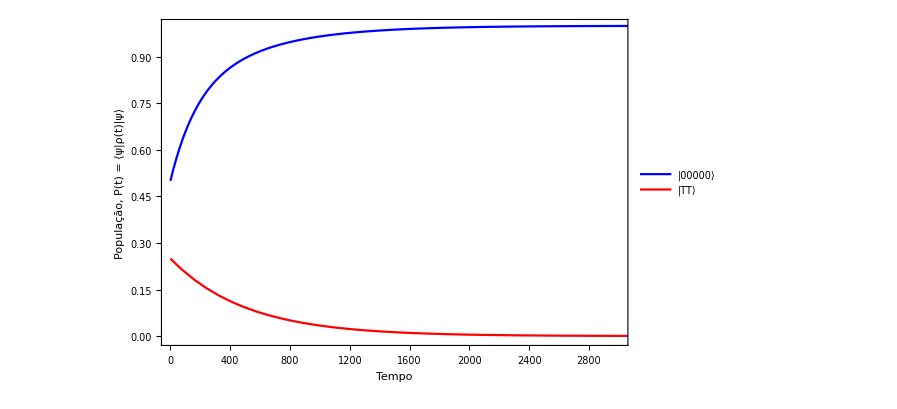

```mathematica
(* Population of the entangled steady-state *)
f[t_]=Simplify[M0000000000[t,γ0,χ0,κ0]];
h[t_]=Chop[Simplify[1/2(M1100011000[t,γ0,χ0,κ0]+M0011000110[t,γ0,χ0,κ0]+2 Re[M1100000110[t,γ0,χ0,κ0]])]];
Plot[{f[t],Chop[h[t]]},{t,0,4000},PlotRange->{{0,3000},{-0.01,1}},Frame->True,PlotStyle->{Blue,Red},FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"|00000⟩", "|TT⟩"},LabelStyle->{Black,14}],{0.9,0.85}],FrameLabel->{"Tempo","População, P(t) = ⟨ψ|ρ(t)|ψ⟩"},LabelStyle->Directive[17,Black]]
```

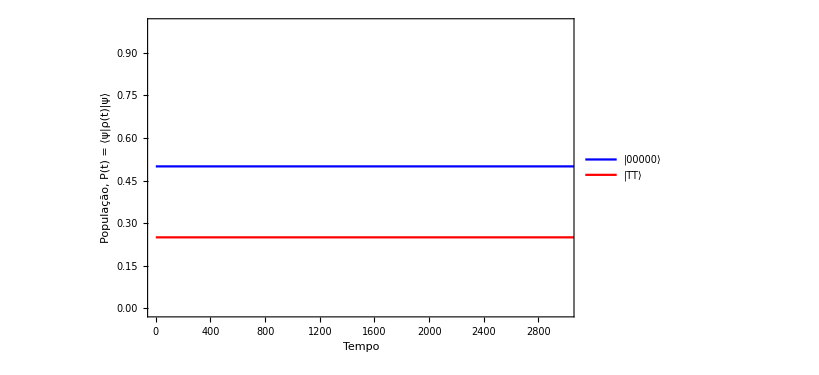

```mathematica
(* Non-dissipative *)
f0[t_]=Simplify[M0000000000[t,0,0,0]];
h0[t_]=Chop[Simplify[1/2(M1100011000[t,0,0,0]+M0011000110[t,0,0,0]+2 Re[M1100000110[t,0,0,0]])]];
Plot[{f0[t],Chop[h0[t]]},{t,0,4000},PlotRange->{{0,3000},{-0.01,1}},Frame->True,PlotStyle->{Blue,Red},FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"|00000⟩", "|TT⟩"},LabelStyle->{Black,14}],{0.9,0.85}],FrameLabel->{"Tempo","População, P(t) = ⟨ψ|ρ(t)|ψ⟩"},LabelStyle->Directive[17,Black]]
```

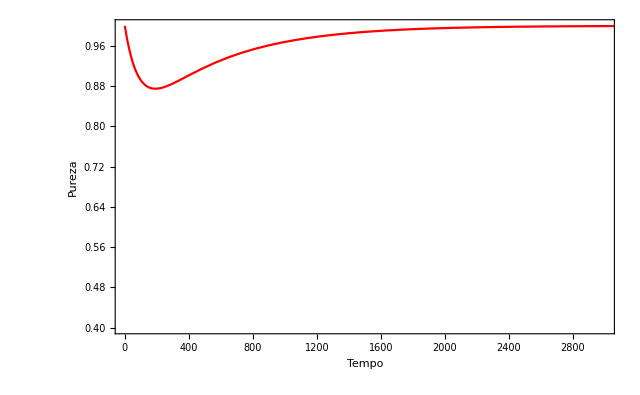

```mathematica
(* Defining the Purity expression *)
P[t_]=Chop[Simplify[M1100011000[t,γ0,χ0,κ0]^2+M0011000110[t,γ0,χ0,κ0]^2+M0000100001[t,γ0,χ0,κ0]^2+M0000000000[t,γ0,χ0,κ0]^2+M1000010000[t,γ0,χ0,κ0]^2+M0100001000[t,γ0,χ0,κ0]^2+M0010000100[t,γ0,χ0,κ0]^2+M0001000010[t,γ0,χ0,κ0]^2+2 M1100000110[t,γ0,χ0,κ0] Conjugate[M1100000110[t,γ0,χ0,κ0]]+2 M1100000001[t,γ0,χ0,κ0] Conjugate[M1100000001[t,γ0,χ0,κ0]]+2 M0011000001[t,γ0,χ0,κ0] Conjugate[M0011000001[t,γ0,χ0,κ0]]+2 M1100000000[t,γ0,χ0,κ0] Conjugate[M1100000000[t,γ0,χ0,κ0]]+2 M0011000000[t,γ0,χ0,κ0] Conjugate[M0011000000[t,γ0,χ0,κ0]]+2 M0000100000[t,γ0,χ0,κ0] Conjugate[M0000100000[t,γ0,χ0,κ0]]]];

Plot[P[t],{t,0,4000},PlotRange->{{0,3000},{0.4,1}},Frame->True,PlotStyle->{Red},FrameTicksStyle->Directive[14,Black],FrameLabel->{"Tempo","Pureza"},LabelStyle->Directive[17,Black]]
```

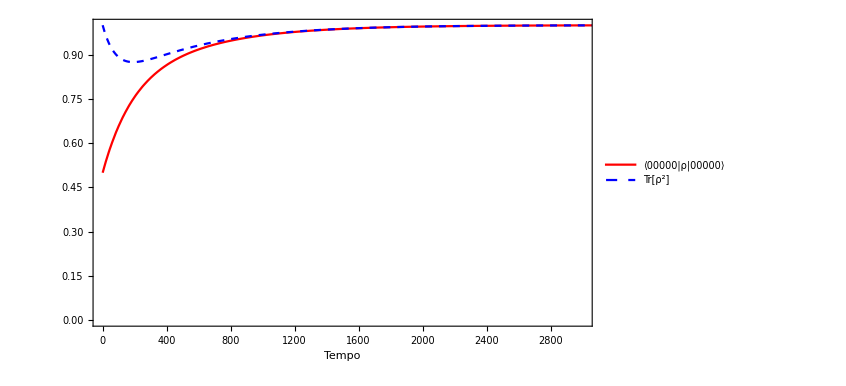

```mathematica
Plot[{f[t],P[t]},{t,0,4000},PlotRange->{{0,3000},{0.,1}},Frame->True,PlotStyle->{Red,{Blue,Dashed}},FrameTicksStyle->Directive[14,Black],FrameLabel->{"Tempo"},LabelStyle->Directive[17,Black],PlotLegends->Placed[LineLegend[{"⟨00000|ρ|00000⟩", "Tr[ρ^2]"},LabelStyle->{Black,14}],{0.78,0.15}]]
```

```mathematica
Clear[γ,κ]
ff[γ_,κ_]=Re[M0000000000[500,γ,0,κ]];

Plot[{ff[γ,0],ff[0,γ]},{γ,0,0.05},PlotRange->{{0,0.05},{0,1}},Frame->True,FrameLabel->{"x","⟨00000|ρ|00000⟩"},LabelStyle->Directive[17,Black],FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"(γ=x,χ=0,κ=0)", "(γ=0,χ=0,κ=x)"},LabelStyle->{Black,14}],{1.0,0.85}]]
```

-Graphics-

```mathematica
(* Population of the entangled steady-state *)
cav[t_]=Re[Simplify[M0000100001[t,γ0,χ0,κ0]]];
ion1[t_]=Re[Simplify[M1100011000[t,γ0,χ0,κ0]]];
ion2[t_]=Re[Simplify[M0011000110[t,γ0,χ0,κ0]]];
Plot[{cav[t],ion1[t],ion2[t]},{t,0,10},PlotRange->{{0,10},{-0.01,1}},Frame->True,PlotStyle->{Blue,Red,Green},FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"⟨00001|ρ|00001⟩", "⟨11000|ρ|11000⟩","⟨00110|ρ|00110⟩"},LabelStyle->{Black,14}],{1.0,0.85}],FrameLabel->{"Tempo","População"},LabelStyle->Directive[17,Black]]
```

-Graphics-

```mathematica
(* Determining the negativity of the ion 1*)
negativity1[t_,γ_,χ_,κ_] = 1/2 Sum[Abs[eigenT1[[i]]]-eigenT1[[i]],{i,1,4}];
eigenvalue11[t_,γ_,χ_,κ_]=eigenT1[[1]];
eigenvalue12[t_,γ_,χ_,κ_]=eigenT1[[2]];
eigenvalue13[t_,γ_,χ_,κ_]=eigenT1[[3]];
eigenvalue14[t_,γ_,χ_,κ_]=eigenT1[[4]];
neg1[t_]=Re@Chop[Simplify[negativity1[t,γ0,χ0,κ0]]];
e11[t_]=Re@eigenvalue11[t,γ0,χ0,κ0];
e12[t_]=Re@eigenvalue12[t,γ0,χ0,κ0];
e13[t_]=Re@eigenvalue13[t,γ0,χ0,κ0];
e14[t_]=Re@eigenvalue14[t,γ0,χ0,κ0];
(* Determining the negativity of the ion 2 *)
negativity2[t_,γ_,χ_,κ_] = 1/2 Sum[Abs[eigenT2[[i]]]-eigenT2[[i]],{i,1,4}];
eigenvalue21[t_,γ_,χ_,κ_]=eigenT2[[1]];
eigenvalue22[t_,γ_,χ_,κ_]=eigenT2[[2]];
eigenvalue23[t_,γ_,χ_,κ_]=eigenT2[[3]];
eigenvalue24[t_,γ_,χ_,κ_]=eigenT2[[4]];
neg2[t_]=Re@Chop[Simplify[negativity2[t,γ0,χ0,κ0]]];
e21[t_]=Re@eigenvalue21[t,γ0,χ0,κ0];
e22[t_]=Re@eigenvalue22[t,γ0,χ0,κ0];
e23[t_]=Re@eigenvalue23[t,γ0,χ0,κ0];
e24[t_]=Re@eigenvalue24[t,γ0,χ0,κ0];
Plot[{e11[t],e12[t],e13[t],e14[t]},{t,0,20},PlotRange->{-1,1},Frame->True,PlotStyle->{Blue,Red,Green,Purple},FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"Eigenvalue 1", "Eigenvalue 2","Eigenvalue 3","Eigenvalue 4"},LabelStyle->{Black,14}],{1.0,0.85}],FrameLabel->{"Tempo","Eigenvalues  of ρ1T2"},LabelStyle->Directive[17,Black]]
Plot[{e21[t],e22[t],e23[t],e24[t]},{t,0,20},PlotRange->{-1,1},Frame->True,PlotStyle->{Purple,Green,Red,Blue},FrameTicksStyle->Directive[14,Black],PlotLegends->Placed[LineLegend[{"Eigenvalue 1", "Eigenvalue 2","Eigenvalue 3","Eigenvalue 4"},LabelStyle->{Black,14}],{1.0,0.85}],FrameLabel->{"Tempo","Eigenvalues  of ρ2T2"},LabelStyle->Directive[17,Black]]
Plot[{neg1[t],neg2[t]},{t,0,20},PlotRange->{-0.01,0.5},Frame->True,PlotStyle->{Darker[Red],Darker[Green]},FrameTicksStyle->Directive[14,Black],FrameLabel->{"Tempo","Negatividade "},LabelStyle->Directive[17,Black],PlotLegends->Placed[LineLegend[{"Íon 1", "Íon 2"},LabelStyle->{Black,14}],{1.0,0.85}]]
```

-Graphics-

-Graphics-

-Graphics-

## 7. Misc.

```mathematica
A=({{a11, a12, a13, a14}, {a21, a22, a23, a24}, {a31, a32, a33, a34}, {a41, a42, a43, a44}})
```

{{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}}

```mathematica
A.A // MatrixForm
```

(a11^2+a12 a21+a13 a31+a14 a41 | a11 a12+a12 a22+a13 a32+a14 a42 | a11 a13+a12 a23+a13 a33+a14 a43 | a11 a14+a12 a24+a13 a34+a14 a44
a11 a21+a21 a22+a23 a31+a24 a41 | a12 a21+a22^2+a23 a32+a24 a42 | a13 a21+a22 a23+a23 a33+a24 a43 | a14 a21+a22 a24+a23 a34+a24 a44
a11 a31+a21 a32+a31 a33+a34 a41 | a12 a31+a22 a32+a32 a33+a34 a42 | a13 a31+a23 a32+a33^2+a34 a43 | a14 a31+a24 a32+a33 a34+a34 a44
a11 a41+a21 a42+a31 a43+a41 a44 | a12 a41+a22 a42+a32 a43+a42 a44 | a13 a41+a23 a42+a33 a43+a43 a44 | a14 a41+a24 a42+a34 a43+a44^2)

```mathematica
Tr[A.A]
```

a11^2+2 a12 a21+a22^2+2 a13 a31+2 a23 a32+a33^2+2 a14 a41+2 a24 a42+2 a34 a43+a44^2

```mathematica
B=({{b11, b12, b13, b14, b15}, {b21, b22, b23, b24, b25}, {b31, b32, b33, b34, b35}, {b41, b42, b43, b44, b45}, {b51, b52, b53, b54, b55}})
```

{{b11,b12,b13,b14,b15},{b21,b22,b23,b24,b25},{b31,b32,b33,b34,b35},{b41,b42,b43,b44,b45},{b51,b52,b53,b54,b55}}

```mathematica
B.B //MatrixForm
```

(b11^2+b12 b21+b13 b31+b14 b41+b15 b51 | b11 b12+b12 b22+b13 b32+b14 b42+b15 b52 | b11 b13+b12 b23+b13 b33+b14 b43+b15 b53 | b11 b14+b12 b24+b13 b34+b14 b44+b15 b54 | b11 b15+b12 b25+b13 b35+b14 b45+b15 b55
b11 b21+b21 b22+b23 b31+b24 b41+b25 b51 | b12 b21+b22^2+b23 b32+b24 b42+b25 b52 | b13 b21+b22 b23+b23 b33+b24 b43+b25 b53 | b14 b21+b22 b24+b23 b34+b24 b44+b25 b54 | b15 b21+b22 b25+b23 b35+b24 b45+b25 b55
b11 b31+b21 b32+b31 b33+b34 b41+b35 b51 | b12 b31+b22 b32+b32 b33+b34 b42+b35 b52 | b13 b31+b23 b32+b33^2+b34 b43+b35 b53 | b14 b31+b24 b32+b33 b34+b34 b44+b35 b54 | b15 b31+b25 b32+b33 b35+b34 b45+b35 b55
b11 b41+b21 b42+b31 b43+b41 b44+b45 b51 | b12 b41+b22 b42+b32 b43+b42 b44+b45 b52 | b13 b41+b23 b42+b33 b43+b43 b44+b45 b53 | b14 b41+b24 b42+b34 b43+b44^2+b45 b54 | b15 b41+b25 b42+b35 b43+b44 b45+b45 b55
b11 b51+b21 b52+b31 b53+b41 b54+b51 b55 | b12 b51+b22 b52+b32 b53+b42 b54+b52 b55 | b13 b51+b23 b52+b33 b53+b43 b54+b53 b55 | b14 b51+b24 b52+b34 b53+b44 b54+b54 b55 | b15 b51+b25 b52+b35 b53+b45 b54+b55^2)

```mathematica
Tr[B.B]
```

b11^2+2 b12 b21+b22^2+2 b13 b31+2 b23 b32+b33^2+2 b14 b41+2 b24 b42+2 b34 b43+b44^2+2 b15 b51+2 b25 b52+2 b35 b53+2 b45 b54+b55^2

```mathematica
c=({{c11, c12, c13, c14, c15, c16}, {c21, c22, c23, c24, c25, c26}, {c31, c32, c33, c34, c35, c36}, {c41, c42, c43, c44, c45, c46}, {c51, c52, c53, c54, c55, c56}, {c61, c62, c63, c64, c65, c66}})
```

{{c11,c12,c13,c14,c15,c16},{c21,c22,c23,c24,c25,c26},{c31,c32,c33,c34,c35,c36},{c41,c42,c43,c44,c45,c46},{c51,c52,c53,c54,c55,c56},{c61,c62,c63,c64,c65,c66}}

```mathematica
Tr[c.c]
```

c11^2+2 c12 c21+c22^2+2 c13 c31+2 c23 c32+c33^2+2 c14 c41+2 c24 c42+2 c34 c43+c44^2+2 c15 c51+2 c25 c52+2 c35 c53+2 c45 c54+c55^2+2 c16 c61+2 c26 c62+2 c36 c63+2 c46 c64+2 c56 c65+c66^2

```mathematica
ff[0.1,0]
```

0.996612-9.48677×10^-20 ⅈ

```mathematica
ff[0,0.2]
```

0.499977+4.85706×10^-17 ⅈ